# How much electricity does my hot tub use?

## Using Smart Meter data to estimate the energy consumption of a hot tub.

Kyle MacLaury

## Introduction

When we purchased our home in 2015 it already had a hot tub installed on the exterior of the  home.  I have always been curious to know how much energy it uses, how much it costs, and what its environmental impact is.  My utility, Green Mountain Power (www.greenmountainpower.com) (insert financial data here) allows it’s customers to download their energy consumption data as a CSV file with their kWh consumption in each 15 minute interval.  Below, I have imported my home’s energy consumption from February 1, 2019 to June 1, 2019 as a Dataset.

```mathematica
usage=SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Homework\\Drafts\\Homework Data.csv"]
```

Dataset[<>]

## Key Facts

Our home is located in Quechee, Vermont a village within the City of Hartford.    The nearest weather station is at the Lebanon Municipal Airport which is 5.6 miles away.

```mathematica
GeoDistance[Entity["Airport","KLEB"],{43.6538820,-72.4092450}]
```

5.60516 mi

```mathematica
GeoGraphics[{Entity["City",{"Hartford","Vermont","UnitedStates"}],GeoRangePadding->None,GeoMarker[Entity["Airport","KLEB"]],GeoMarker[{43.6538820,-72.4092450},"Color"->Green]}]
```

-Graphics-

Based on a review of the manufacturer’s Owner’s Manuals the capacity of the hot tub is 1,500 Liters.  Based on observations of the hot tub has both a constant electrical load, and intermittent loads.  The constant load consists of a circulation pump, sensors and operational control panel.  The primary intermittent load is an electric resistance heating element that operates when necessary to maintain the hot tub temperature.

```mathematica
hottubvolume=Quantity[1500,"Liters"]
```

1500 L

In addition to the hot tub, our home has two additional very large loads that complicate the analysis.  One of those loads is a Nissan Leaf which we don’t charge daily.  On those days that it is charged it is common for it to consume between 10 to 20 kWh over the course of many hours.  The other very large load is a sauna, which is used infrequently, and only for an hour or two at a time.  To arrive at an accurate estimate of the hot tub’s energy consumption it may be necessary to eliminate days from consideration during which the electric car or sauna used a significant amount of energy.

## Experimental Conditions

The hot tub was filled and operating through the winter of 2018 to 2019.  The hot tub was drained, and its breaker opened to prevent electricity consumption on April 14, 2019.  It remained empty and unpowered until it was refilled on May 11, 2019.

```mathematica
hottubOn1=DayRange[DateObject[{2019,2,1}],DateObject[{2019,4,14}], "Day"];
hottubOff=DayRange[DateObject[{2019,4,15}],DateObject[{2019,5,10}], "Day"];
hottubRefill=DateObject[{2019,5,11}];
hottubOn2=DayRange[DateObject[{2019,5,12}],DateObject[{2019,6,1}],"Day"];
```

## Data Wrangling

### Usage Data

To analyze the data it is helpful to transform the original data format to a TimeSeries.

```mathematica
usageTS=TimeSeries @ Map[
	{#["IntervalStart"], #["Quantity"]} &,
	Normal[usage]
]
```

TimeSeries[…]

Visualizing the data is now simple.  Note that the period during which the hot tub was unplugged, from mid-April to mid-May appears to have lower energy consumption than the periods during which it was operating.

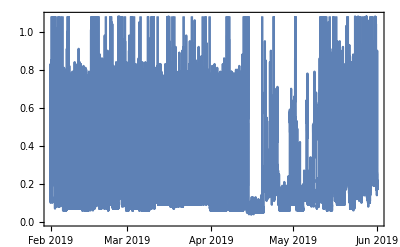

```mathematica
DateListPlot[usageTS]
```

TimeSeries objects allow simple transformations of the data, for instance calculating a daily usage value from 15 minute interval data.

```mathematica
dailyUsage=TimeSeriesAggregate[usageTS,"Day",Total]
```

TimeSeries[…]

### Weather Data

The daily average daily temperature for the nearest weather station is available natively.

```mathematica
klebMeanDailyTemp=WeatherData["KLEB", "MeanTemperature", {{2019, 2, 1}, {2019,5,31},"Day"}]
```

TimeSeries[…]

The two time series can be plotted together easily.

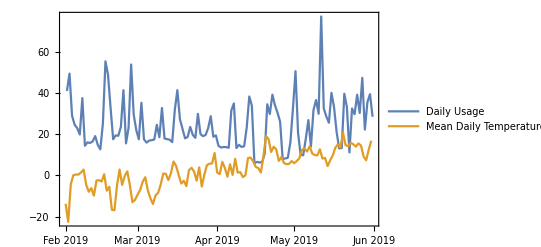

```mathematica
DateListPlot[{dailyUsage,klebMeanDailyTemp},PlotLegends->{"Daily Usage","Mean Daily Temperature"}]
```

The data can also be combined into a TemporalData structure as well.

```mathematica
usagandTempTemporalData=TemporalData[{dailyUsage,klebMeanDailyTemp}]
```

TemporalData[…]

```mathematica
DateListPlot[usagandTempTemporalData,PlotLegends->{"Daily Usage","Mean Daily Temperature"}]
```

-Graphics-

## Viewing Daily Patterns

It is helpful to view the detailed consumption pattern for each day.  This allows for visual search of patterns attributable to the hot tub’s energy consumption, and allows for determination of days during which the Nissan Leaf was plugged in.

```mathematica
toDate[dateObject_DateObject] := DateObject[DateValue[dateObject, {"Year", "Month", "Day"}]];
```

```mathematica
regroupdata[objects_] := DateListPlot[TimeSeries @ Map[
	{#["IntervalStart"], #["Quantity"]} &,
	objects
]]


allplots = GroupBy[
	Normal[usage], 
	toDate[#IntervalStart] &,
regroupdata
];
```

```mathematica
Manipulate[
allplots[date],
{date, Keys[allplots]}
]
```

The y-axis of each day’s energy consumption plot indicates the kWh energy consumption within a 15 minute interval.

A visual inspection of each day’s energy consumption yields a number of interesting observations.  First, the energy consumption has a baseline in the range of  approximately 0.1 to 0 .2 kWh per fifteen minutes when the hot tub is operating.  Also of note when the hot tub is operating are the periodic spikes in consumption throughout the day.  These spikes are presumably the electric resistance heating element responsible for heating the hot tub’s water.  These spikes are noticeably absent during the period that the hot tub is off.  The baseline consumption is also noticeably lower while the hot tub is off.  During that time the baseline appears to be closer to 0.05 kWh per 15 minutes.   

By chance, the daily consumption of February 1 illustrates the primary features that allow a determination of those days during which the Nissan Leaf was charged, or the sauna was used.  When the Nissan Leaf is charged the baseline shifts noticeably higher to approximately 0.5 kWh per 15 minutes, as can be seen from approximately 17:00 on February 1. The sauna’s consumption goes as high as 1.5 kWh per 15 minutes, as can be seen at approximately 09:00 on February 1.

While not perfect, visual inspection of the data allows a determination of those days during which the Nissan Leaf was unplugged, or the sauna was used.  Those days are indicated below by the variable “evDays”.

```mathematica
evDays={DateObject[{2019,2,1}],DateObject[{2019,2,2}],DateObject[{2019,2,3}],DateObject[{2019,2,6}],DateObject[{2019,2,7}],DateObject[{2019,2,15}],DateObject[{2019,2,16}],DateObject[{2019,2,17}],DateObject[{2019,2,22}],DateObject[{2019,2,23}],DateObject[{2019,2,25}],DateObject[{2019,2,26}],DateObject[{2019,3,2}],DateObject[{2019,3,15}],DateObject[{2019,3,16}],DateObject[{2019,3,2}],DateObject[{2019,4,6}],DateObject[{2019,4,7}],DateObject[{2019,4,12}],DateObject[{2019,4,13}],DateObject[{2019,4,14}],DateObject[{2019,4,20}],DateObject[{2019,4,21}],DateObject[{2019,4,22}],DateObject[{2019,4,23}],DateObject[{2019,4,24}],DateObject[{2019,4,25}],DateObject[{2019,4,29}],DateObject[{2019,4,30}],DateObject[{2019,5,1}],,DateObject[{2019,5,1}],DateObject[{2019,5,6}],DateObject[{2019,5,8}],DateObject[{2019,5,9}],DateObject[{2019,5,10}],DateObject[{2019,5,11}],DateObject[{2019,5,12}],DateObject[{2019,5,13}],DateObject[{2019,5,14}],DateObject[{2019,5,15}],DateObject[{2019,5,16}],DateObject[{2019,5,17}],DateObject[{2019,5,20}],DateObject[{2019,5,21}],DateObject[{2019,5,23}],DateObject[{2019,5,24}],DateObject[{2019,5,25}],DateObject[{2019,5,29}],DateObject[{2019,5,30}]};
```

## Pulling it all together

```mathematica
AssociationThread[usagandTempTemporalData["Dates"]->(AssociationThread[{"Daily Usage","Daily Temperature"}->#]&/@Transpose[usagandTempTemporalData["ValueList"]])]//Dataset
```

Dataset[<>]